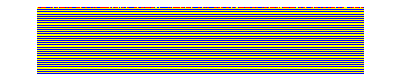
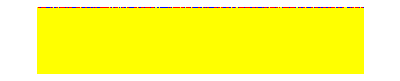
{{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

```mathematica
ParallelTable[ BlockRandom[SeedRandom[828];
				ArrayPlot[
		CellularAutomaton[{FromDigits[Tuples[{1,0},7]/. {l1_,l3_,b3_,c_,b1_,r1_,r3_}:>If[If[c==i,r1+r3,l1+l3,b1+b3]+c>=3,2,1,0],2],3,k},

RandomChoice[{.4,.5, .1}->{2,1,0},300],60],

ColorRules->{0-> Yellow ,1->Red, 2 -> Blue},Frame->False]],{i,4},{k,3,6}]
```

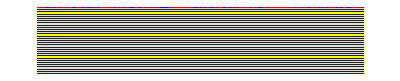
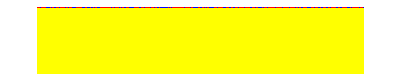
{{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

```mathematica
ParallelTable[ BlockRandom[SeedRandom[828];
				ArrayPlot[
	CellularAutomaton[{FromDigits[Tuples[{1,0},7]/. {l1_,l3_,b3_,c_,b1_,r1_,r3_}:>If[If[c==i,r1+r3,l1+l3,b1+b3]+c>=3,2,1,0],2],3,k},

RandomChoice[{.4,.6, 0.}->{2,1,0},300],60],

ColorRules->{0-> Yellow ,1->Red, 2 -> Blue},Frame->False]],{i,4},{k,3,6}]
```

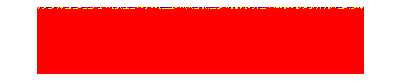
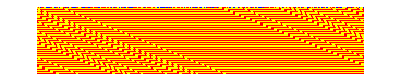
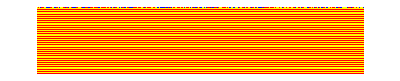
{{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-}}

```mathematica
Table[BlockRandom[SeedRandom[828];
				ArrayPlot[
CellularAutomaton[{FromDigits[Tuples[{1,0},7]/. {r1_,b3_, c_,l1_,l3_,b1_,r3_}:>If[If[c==k,r1+r3 ,l1+l3 ,b1+b3]+c>3,2,1,0],3],3,i},

RandomChoice[{.3,.4, .3}->{2,1,0},300],60],

ColorRules->{0-> Yellow ,1->Red, 2 -> Blue},Frame->False]],{k,1,4},{i,2 ,4}]
```

```mathematica
FromDigits[Tuples[{2,1,0},7]]
```

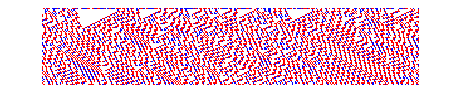
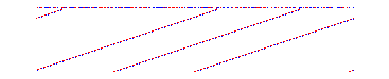
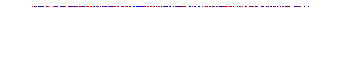
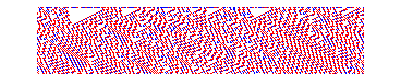
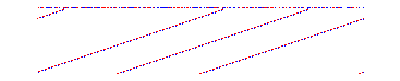
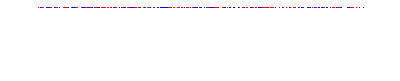
{{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-}}

```mathematica
Table[BlockRandom[SeedRandom[828];
				ArrayPlot[
CellularAutomaton[{FromDigits[Tuples[{0,1},7]/. {r1_,r3_,b3_, c_,l1_,l3_,b1_}:>If[If[c==k,r1+r3 ,l1+l3 ,b1+b3]+c>3,2,1],2],3,i},

RandomChoice[{.4,.3,.3}->{2,1,0},300],60],

ColorRules->{1->Red, 2 -> Blue},Frame->False]],{k,1,4},{i,2 ,4}]
```

```mathematica
BlockRandom[SeedRandom[828];
				ArrayPlot[
CellularAutomaton[{FromDigits[Tuples[{1,0},7]/. {r1_,b3_,l3_, c_,l1_,b1_,r3_}:>If[If[c==0,r1+r3 ,l1+l3 ,b1+b3]+c>3,2,1,0],2],3,3},

RandomChoice[{.3333,.3333, .3333}->{2,1,0},300],60],

ColorRules->{0-> Yellow ,1->Red, 2 -> Blue},Frame->False]]
```

-Graphics-

```mathematica
BlockRandom[SeedRandom[828];
				ArrayPlot[
CellularAutomaton[{FromDigits[Tuples[{1,0},7]/. {a1_,a2_,a3_,a4_,a5_,a6_,a7_}->If[If[a4==0,a1+a3+a4,a4+a5+a7]≥2,1,0],2],3,3},

RandomChoice[{.4,.5, .1}->{2,1,0},300],60],

ColorRules->{0-> Yellow ,1->Red, 2 -> Blue},Frame->False]]
```

-Graphics-

```mathematica
Table[BlockRandom[SeedRandom[24425];
ArrayPlot[CellularAutomaton[{FromDigits[Tuples[{1,0},7]/. {l3_,_,l1_,c_,r1_,_,r3_}:>If[If[c==i,r1+r3,l1+l3]+c>=2,1,0],2],2,3},RandomChoice[{.5,.5}->{1,0},1000],500],ColorRules->{0->Yellow,1->Red},Frame->False]],{i,1,3}]
```

{-Graphics-,-Graphics-,-Graphics-}

searching for all 2^32 radius-2 rules --> achieves “approximate consensus”
below : the cells go to the “majority value” (this is the r = 2 rule 4196304428, for p = 0.6):

```mathematica
BlockRandom[SeedRandom[567]; 
 ArrayPlot[
  CellularAutomaton[{4196304428, 2, 2}, 
   RandomChoice[{.6, .4} -> {1, 0}, 500], 200], 
  ColorRules -> {0 -> Yellow, 
    1 ->  Red}, Frame -> False]]
```

-Graphics-

rule 184: doesn’t achieve consensus on “overall density”, but does do so with respect to left- and right-moving stripes, here with the nested pattern generated when p = 0.5:

```mathematica
BlockRandom[SeedRandom[567];
ArrayPlot[CellularAutomaton[184,RandomChoice[{1,0},400],180],ColorRules->{0->Yellow,1->Red},Frame->False]]
```

-Graphics-

Achieving consensus faster: comparison of GKL rule with another radius - 3 rule, latter has shorter average consensis time:

```mathematica
Column[BlockRandom[SeedRandom[24125];
ArrayPlot[CellularAutomaton[#,RandomChoice[{.5,.5}->{1,0},800],240],ColorRules->{0->Yellow,1->Red},Frame->False,ImageSize->{650,Automatic}]]&/@{{337607298446901146542393000444934784552,2,3},{338557163619953682141694933300561896488,2,3},{313421633154342960352882914658469183496,2,3}}]
```

-Graphics-
-Graphics-
-Graphics-

```mathematica
Column[BlockRandom[SeedRandom[24125];
ArrayPlot[CellularAutomaton[#,RandomChoice[{.5,.5}->{1,0},800],240],ColorRules->{0->Yellow,1->Red},Frame->False,ImageSize->{650,Automatic}]]&/@{{337607298446901146542393000444934784552,2,3},{338557163619953682141694933300561896488,2,3},{313421633154342960352882914658469183496,2,3}}]
```

-Graphics-
-Graphics-
-Graphics-

A more elaborate / ornate way

```mathematica
Column[BlockRandom[SeedRandom[24125];
ArrayPlot[CellularAutomaton[#,RandomChoice[{.6,.4}->{1,0},800],240],ColorRules->{0->Yellow,1->Red},Frame->False,ImageSize->{650,Automatic}]]&/@{{337607298446901146542393000444934784552,2,3},{338557163619953682141694933300561896488,2,3},{313421633154342960352882914658469183496,2,3}}]
```

-Graphics-
-Graphics-
-Graphics-

```mathematica
Column[BlockRandom[SeedRandom[24125];
ArrayPlot[CellularAutomaton[#,RandomChoice[{.49,.51}->{1,0},800],240],ColorRules->{0->Yellow,1->Red},Frame->False,ImageSize->{650,Automatic}]]&/@{{337607298446901146542393000444934784552,2,3},{338557163619953682141694933300561896488,2,3},{313421633154342960352882914658469183496,2,3}}]
```

-Graphics-
-Graphics-
-Graphics-

```mathematica
Column[BlockRandom[SeedRandom[24125];
ArrayPlot[CellularAutomaton[#,RandomChoice[{.1,.4,.5}->{2,1,0},800],240],ColorRules->{0->Yellow,1->Red,2-> Blue},Frame->False,ImageSize->{650,Automatic}]]&/@{{337607298446901146542393000444934784552,3,3},{338557163619953682141694933300561896488,3,3},{313421633154342960352882914658469183496,3,3}}]
```

-Graphics-
-Graphics-
-Graphics-

```mathematica
Column[BlockRandom[SeedRandom[24125];
ArrayPlot[CellularAutomaton[#,RandomChoice[{.1,.5,.4}->{2,1,0},800],240],ColorRules->{0->Yellow,1->Red,2-> Blue},Frame->False,ImageSize->{650,Automatic}]]&/@{{337607298446901146542393000444934784552,3,5},{338557163619953682141694933300561896488,3,5},{313421633154342960352882914658469183496,3,5}}]
```

-Graphics-
-Graphics-
-Graphics-

```mathematica
Column[BlockRandom[SeedRandom[24125];
ArrayPlot[CellularAutomaton[#,RandomChoice[{.38,.22,.4}->{2,1,0},800],240],ColorRules->{0->Yellow,1->Red,2-> Blue},Frame->False]]&/@{{337607298446901146542393000444934784552,3,4},{338557163619953682141694933300561896488,3,4},{313421633154342960352882914658469183496,3,4}}]
```

-Graphics-
-Graphics-
-Graphics-

```mathematica
Column[BlockRandom[SeedRandom[24125];
ArrayPlot[CellularAutomaton[#,RandomChoice[{.22,.38,.4}->{2,1,0},800],240],ColorRules->{0->Yellow,1->Red,2-> Blue},Frame->False]]&/@{{337607298446901146542393000444934784552,3,4},{338557163619953682141694933300561896488,3,4},{313421633154342960352882914658469183496,3,4}}]
```

-Graphics-
-Graphics-
-Graphics-

```mathematica
Column[BlockRandom[SeedRandom[24125];
ArrayPlot[CellularAutomaton[#,RandomChoice[{.22,.38,.4}->{2,1,0},800],240],ColorRules->{0->Yellow,1->Red,2-> Blue},Frame->False]]&/@{{337607298446901146542393000444934784552,3,3},{338557163619953682141694933300561896488,3,3},{313421633154342960352882914658469183496,3,3}}]
```

-Graphics-
-Graphics-
-Graphics-

```mathematica
Column[BlockRandom[SeedRandom[24125];
ArrayPlot[CellularAutomaton[#,RandomChoice[{.1,.5,.4}->{2,1,0},800],240],ColorRules->{0->Yellow,1->Red,2-> Blue},Frame->False,ImageSize->{650,Automatic}]]&/@{{337607298446901146542393000444934784552,3,3},{338557163619953682141694933300561896488,3,3},{313421633154342960352882914658469183496,3,3}}]
```

-Graphics-
-Graphics-
-Graphics-

```mathematica
Column[BlockRandom[SeedRandom[24125];
ArrayPlot[CellularAutomaton[#,RandomChoice[{.1,.45,.45}->{2,1,0},800],240],ColorRules->{0->Yellow,1->Red,2-> Blue},Frame->False,ImageSize->{650,Automatic}]]&/@{{337607298446901146542393000444934784552,3,3},{338557163619953682141694933300561896488,3,3},{313421633154342960352882914658469183496,3,3}}]
```

-Graphics-
-Graphics-
-Graphics-

```mathematica
Column[BlockRandom[SeedRandom[24125];
ArrayPlot[CellularAutomaton[#,RandomChoice[{.1,.5,.4}->{2,1,0},800],240],ColorRules->{0->Yellow,1->Red,2-> Blue},Frame->False,ImageSize->{650,Automatic}]]&/@{{33760798979878444934784552,3,3},{3385548979848498882141694933300561896488,3,3},{3134984894814658469183496,3,3}}]
```

-Graphics-
-Graphics-
-Graphics-

Some rules (e.g. optimal sorting rules):  optimal rules will often be ones that don’t look simple in their behavior, and that can’t realistically be constructed by standard engineering methods, 
and essentially just have to be found “experimentally” by searching the computational universe of possible rules.

```mathematica
Column[BlockRandom[SeedRandom[24125];
ArrayPlot[CellularAutomaton[#,RandomChoice[{.33333,.33333,.33333}->{2,1,0},400],50],ColorRules->{0->Yellow,1->Red,2-> Blue},Frame->False,ImageSize->{650,Automatic}]]&/@{{98981519979879879879818418,3,3},{489895877987878979878988,3,3},{313987987987987987982796,3,3}}]
```

-Graphics-
-Graphics-
-Graphics-

```mathematica
Column[BlockRandom[SeedRandom[24125];
ArrayPlot[CellularAutomaton[#,RandomChoice[{.33333,.33333,.33333}->{2,1,0},400],50],ColorRules->{0->Yellow,1->Red,2-> Blue},Frame->False,ImageSize->{650,Automatic}]]&/@{{989815199712345678765432418,3,3},{4898958772345675432878979878988,3,3},{313982342463773398749837446,3,3}}]
```

-Graphics-
-Graphics-
-Graphics-

```mathematica
Column[BlockRandom[SeedRandom[24125];
ArrayPlot[CellularAutomaton[#,RandomChoice[{.33333,.33333,.33333}->{2,1,0},400],50],ColorRules->{0->Yellow,1->Red,2-> Blue},Frame->False,ImageSize->{650,Automatic}]]&/@{{989815174893039791740140174104718,3,3},{482428442984434242432428988,3,3},{31398238892749872983479827436,3,3}}]
```

-Graphics-
-Graphics-
-Graphics-

```mathematica
Column[BlockRandom[SeedRandom[24125];
ArrayPlot[CellularAutomaton[#,RandomChoice[{.33333,.33333,.33333}->{2,1,0},400],50],ColorRules->{0->Yellow,1->Red,2-> Blue},Frame->False,ImageSize->{650,Automatic}]]&/@{{989815174893039791740140174104718,3,3},{482428442984434242432428988,3,3},{31398238892749872983479827436,3,8}}]
```

-Graphics-
-Graphics-
-Graphics-

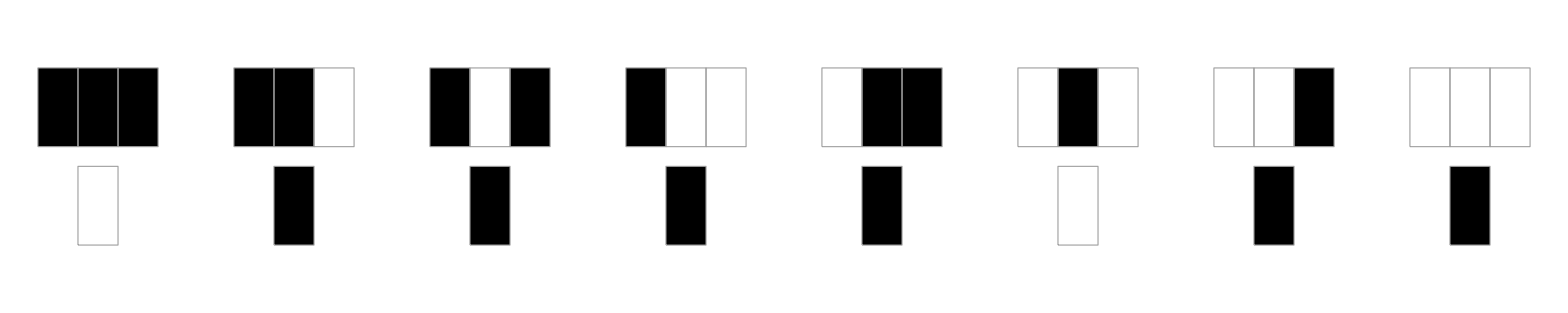

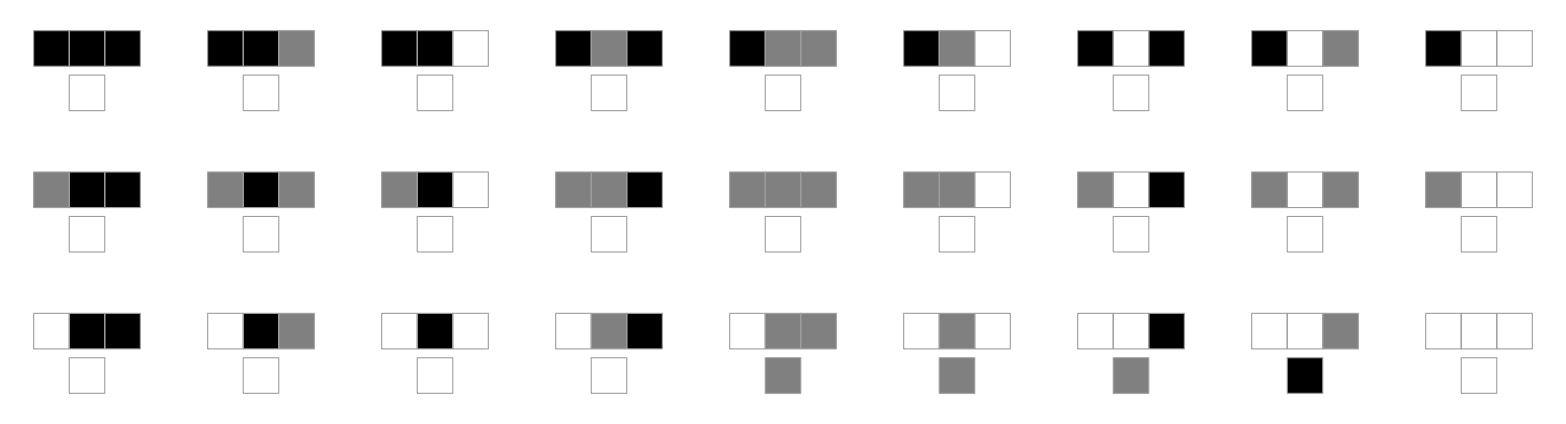

```mathematica
RulePlot@CellularAutomaton[{123,2}]
RulePlot@CellularAutomaton[{123,3}]
```

```mathematica
IntegerDigits[ruleNumber,numColors,numColors^3]
```